```mathematica
Clear["Global`*"]
U[x_] := a x^2 Exp[-b x^2] /. {a-> π/3, b -> 2/(E + π)}
range = 7;
PotData  = Table[{x,U[x]} , {x,-range,range,0.2}];
H [p_,x_] = p^2 / (2 m) + U[x] /. (m-> 1);
KinData = Table[{x,(SolveValues[H[p,x]==3,p][[2]])^2 /2} , {x,-7,7,0.1}];
pltEnergy = ListLinePlot[{PotData,KinData} , PlotLabels->{"Potential"  , "Kinetic"}]
```

-Graphics-

{0,-√((ⅇ+π)/2),√((ⅇ+π)/2)}

{(π x^2)/3,(π (ⅇ+π))/(6 ⅇ)-(2 π (√((ⅇ+π)/2)+x)^2)/(3 ⅇ),(π (ⅇ+π))/(6 ⅇ)-(2 π (-√((ⅇ+π)/2)+x)^2)/(3 ⅇ)}

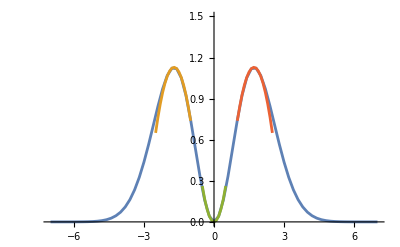

```mathematica
Critpoints = SolveValues[D[U[x] , x]  ==0 , x , Reals]
Taylorseries[x_] = Normal[Series[U[x],{x,#,2}]] &/@ Critpoints
Taylordata1 = Table[{x,Taylorseries[x][[2]]} , {x,-2.5,-1,0.1}];
Taylordata2 = Table[{x,Taylorseries[x][[1]]} , {x,-0.5,0.5,0.1}];
Taylordata3 = Table[{x,Taylorseries[x][[3]]} , {x,1,2.5,0.1}];
ListLinePlot[{PotData,Taylordata1 , Taylordata2 , Taylordata3} , PlotRange->{{-7,7},{0,1.5}}]
```

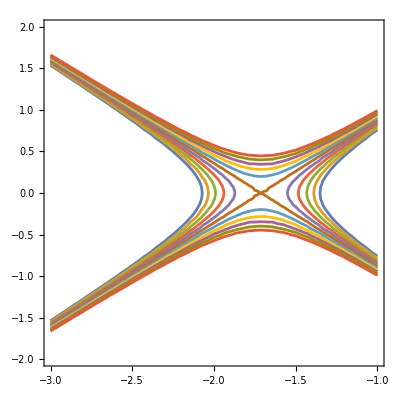

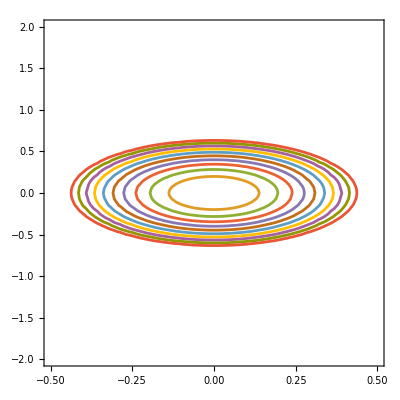

```mathematica
maxEnergy = U[Critpoints[[2]]];
energy1[p_,x_] = Taylorseries[x][[2]] + p^2 /2;
phase1 = Table[energy1[p,x]== e1, {e1,maxEnergy- 0.1  , maxEnergy + 0.1, 0.02}];
plt1 = ContourPlot[Evaluate[phase1] , {x,-3,-1} , {p,-2,2}]
energy2[p_,x_] = Taylorseries[x][[1]] + p^2 /2;
phase2 = Table[energy2[p,x] == e1, { e1, 0, 0.2 , 0.02}];
plt2 = ContourPlot[Evaluate[phase2] , {x,-0.5,0.5},{p,-2,2}]
```

```mathematica
Hamiltonian[p_,x_] = p^2 /2  + U[x];
vctr[x_] = -D[Hamiltonian[p,x],x];
vctrPlot = StreamPlot[{p,vctr[x] } , {x,-range,range} , {p,-range,range}];
```

```mathematica
EqnMotion1 := {y''[t]== -D[U[y[t]],y[t]], y'[0] ==0 , y[0] == 1};
Solution1 = NDSolveValue[EqnMotion1 ,{y[t],y'[t]},{t,0,20}];
x1[t_] = Solution1[[1]];
v1[t_] = Solution1[[2]];
EqnData1 = Table[{x1[t],v1[t]} , {t,0,20,0.1}];

EqnMotion2 := {z''[t]== -D[U[z[t]],z[t]], z'[0] ==2 , z[0] == -7};
Solution2 = NDSolveValue[EqnMotion2 ,{z[t],z'[t]},{t,0,20}];
x2[t_] = Solution2[[1]];
v2[t_] = Solution2[[2]];
EqnData2 = Table[{x2[t],v2[t]}, {t,0,10,0.1}];
EqnPlot = ListLinePlot[{EqnData1,EqnData2}];
```

```mathematica
CoupledEquation1:= {v3'[t] == -D[U[x3[t]],x3[t]] , x3'[t]== v3[t],x3[0] == -7,v3[0] == 3 };
{x3[t_],v3[t_]}  = NDSolveValue[CoupledEquation1,{x3[t],v3[t]},{t,0,20}];
EqnData3 = Table[{x3[t],v3[t]}, {t,0,10,0.1}];

CoupledEquation2:= {v4'[t] == -D[U[x4[t]],x4[t]] , x4'[t]== v4[t],x4[0] == -7,v4[0] == 1 };
{x4[t_],v4[t_]}  = NDSolveValue[CoupledEquation2,{x4[t],v4[t]},{t,0,20}];
EqnData4 = Table[{x4[t],v4[t]}, {t,0,10,0.1}];
```

```mathematica
CoupledPlot = ListLinePlot[{EqnData3,EqnData4}, PlotRange->{{-7,7} , {-1.5,3.2}}];
```

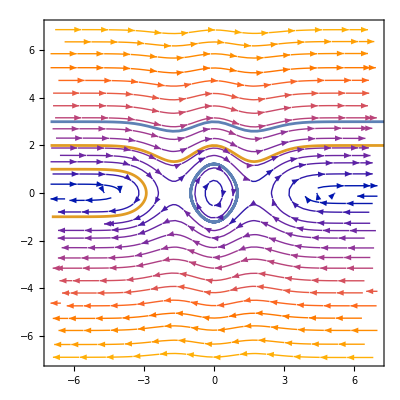

```mathematica
Show[vctrPlot,EqnPlot,CoupledPlot]
```